# Operating with the Fresco files

## Setting current directory, file names etc.

```mathematica
frescoExe=If[$OperatingSystem=="Windows","frescoWin.exe"]
```

frescoWin.exe

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\CAMPIT\Documents\GitHub\bsmllh\nb\fresco

```mathematica
FileNames["*in","C:\\Users\\CAMPIT\\Documents\\GitHub\\bsmllh\\nb\\fresco",2];
currectFile=%
directoryName=DirectoryName[currectFile⟦1⟧]
```

{C:\Users\CAMPIT\Documents\GitHub\bsmllh\nb\fresco\examples\B5-example-tr.in}

C:\Users\CAMPIT\Documents\GitHub\bsmllh\nb\fresco\examples\

## Run fresco

```mathematica
StringJoin[frescoExe," < ", currectFile, " > ",StringDrop[currectFile,-3],".out" ]
Run[% ]
```

frescoWin.exe < C:\Users\CAMPIT\Documents\GitHub\bsmllh\nb\fresco\examples\B5-example-tr.in > C:\Users\CAMPIT\Documents\GitHub\bsmllh\nb\fresco\examples\B5-example-tr.out

0

## Plot and Export calculated Data

```mathematica
plotFromFile[fileName_,expData_:False]:=If[FileExistsQ["fort.201"],
Module[{importedData,plotData,labelPlot,plot,subLabelPlot,exp},
importedData=Import[fileName,"Table"];
plotData=Cases[importedData,{_Real,_Real}];
labelPlot=Cases[importedData,{"@subtitle",__}];
labelPlot=Flatten[Drop[labelPlot,None,1]];
subLabelPlot=Flatten[Cases[importedData,{"#legend",__}]];
labelPlot=StringJoin[labelPlot,"\n",subLabelPlot⟦4⟧];
plot=ListLogPlot[plotData,Joined->True,Frame->True,AspectRatio->1.3,FrameLabel->{"θ_cm, degree","dΩ/dσ, mb/sr"},ImageSize->Medium,PlotLabel->labelPlot];
exp=Export[StringJoin[directoryName,StringReplace[fileName,"."->""],".pdf"],plot,"PDF"];
Print[plot];
]];
```

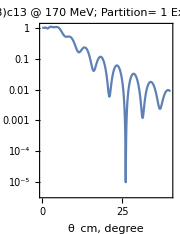

```mathematica
plotFromFile["fort.201"]
```

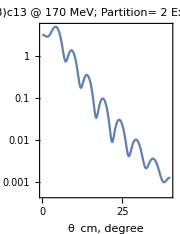

```mathematica
plotFromFile["fort.202"]
```

```mathematica
(*Run["del fort.*"]*)
```